## Argon

### Definitions

```mathematica
hc=1973.32 (* eV*A *);
me=0.511 10^6 (* eV *);
al=0.00729735;
c=3 10^18 (* A/s *);
kB=1.38 10^-23;
aB=hc/(me al) (* A *);
Rmax=20;
Patm=101325;
```

```mathematica
p[e_]:=√(2me e)
```

```mathematica
Off[NDSolveValue::precw]
ParallelEvaluate[Off[NDSolveValue::precw]];
```

```mathematica
Z=18;
T=87;
Pbar=1;
P=Pbar Patm;
Nat=10^-30 P/(kB T) (* A^-3 *);
```

```mathematica
{R,ad,aq,d}= {0.2466248878404586,10.500792442983645,200.50473249410297,2.3812682524175113};
```

```mathematica
Utab={#[[1]],-#[[2]]}&/@Import[FileNameJoin[{NotebookDirectory[],"ArgonPotential.csv"}]][[;;,{1,3}]];
```

```mathematica
UtabInt[r_]=Interpolation[Utab,Method->"Spline"][r];
```

```mathematica
Uc[R_,r_]=Piecewise[{{UtabInt[r], R<r<20}, {0, r>20}, {-Z/r+Z/R+UtabInt[R], True}}];
Uc[r_]=Uc[R,r];
```

```mathematica
Upol[r_]=-ad/(2(r^2+d^2)^2)-aq/(2(r^3+d^3)^2);
```

```mathematica
Ur1[r_?NumericQ]=Piecewise[{{1/r, r≠0}, {0, True}}];
Ur2[r_?NumericQ]=Piecewise[{{1/r^2, r≠0}, {0, True}}];
```

```mathematica
U[r_?NumericQ]=me al^2(Piecewise[{{Uc[r/aB], r≠0}, {0, True}}]+Upol[r/aB]);
dU[r_?NumericQ]=(me al^2)/aB(Piecewise[{{Uc'[r/aB], r≠0}, {0, True}}]+Upol'[r/aB]);
```

```mathematica
EQ[l_,e_,f_, r_]:=-hc^2/(2me)f''[r]-(2l hc^2)/(2me)Ur1[r]f'[r]+(2l hc^2)/(2me)Ur2[r]f[r]+U[r]f[r]==p[e]^2/(2me)f[r]
```

```mathematica
(* SetSharedFunction[dsdw, RadialF] *)
(* Define radial functions RadialF *)
RadialF[l_, r_, En_] := Module[{sol, Ras, vals},
sol[rad_]=rad^l NDSolveValue[{EQ[l,En,f, rad],f[0]==0,f'[0]==1},f[rad],{rad,0,Rmax},WorkingPrecision->20];
Ras[rad_]=1/(√S)(p[En]rad)/hc(SphericalHankelH2[l,(p[En]rad)/hc]+S SphericalHankelH1[l,(p[En]rad)/hc]);
vals=SolveValues[{A sol[Rmax]==Ras[Rmax],A sol'[Rmax]==Ras'[Rmax]},{A,S}][[1]];
vals[[1]]sol[r]
];
(* Define NBrS differential cross section (spectrum) dsdw[En,ω] *)
wdsdw[En_?NumericQ, ω_ ?NumericQ, pol_?BooleanQ] := Module[ {Ri, Rf, M0, dM, M},
If[ω+0.001>=En,Return[0.0]];
Do [
Ri[l,r_]=RadialF[l, r, En];
Rf[l,r_]=RadialF[l, r, En - ω];
,{l,0,3}];
Do[
	M0[l+1,l]=hc/(p[En]p[En-ω])NIntegrate[Rf[l+1,r]Ri[l,r]dU[r],{r,0,Rmax},Method->"LocalAdaptive",PrecisionGoal->5, MaxRecursion->12] (* A *);
	M0[l,l+1]=hc/(p[En]p[En-ω])NIntegrate[Rf[l,r]Ri[l+1,r]dU[r],{r,0,Rmax},Method->"LocalAdaptive",PrecisionGoal->5, MaxRecursion->12] (* A *);
	If[pol,
	dM[l+1,l]=hc/(p[En]p[En-ω])NIntegrate[Rf[l+1,r]Ri[l,r](-ad(me ω^2)/(r^2+d^2 aB^2)aB^3/hc^2),{r,0,Rmax},Method->"LocalAdaptive",PrecisionGoal->5, MaxRecursion->12] (* A *);
	dM[l,l+1]=hc/(p[En]p[En-ω])NIntegrate[Rf[l,r]Ri[l+1,r](-ad(me ω^2)/(r^2+d^2 aB^2)aB^3/hc^2),{r,0,Rmax},Method->"LocalAdaptive",PrecisionGoal->5, MaxRecursion->12] (* A *);
	M[l+1,l]=M0[l+1,l]+dM[l+1,l];
	M[l,l+1]=M0[l,l+1]+dM[l,l+1];
	,
	M[l+1,l]=M0[l+1,l];
	M[l,l+1]=M0[l,l+1];]
,{l,0,2}];
		
2/3 al p[En-ω]/p[En] Sum[(l+1)(Abs[M[l+1,l]]^2+Abs[M[l,l+1]]^2),{l,0,2}]
];
dsdw[En_?NumericQ, ω_ ?NumericQ, pol_?BooleanQ] := wdsdw[En, ω, pol]/ω;
```

### Kinetics

```mathematica
EdNRange=Join[{0.1,0.3,9,10},Range[0.5,8,0.5]]//Sort;
EEDFData=Import[FileNameJoin[{NotebookDirectory[],"eedfsArgon.dat"}]];
Do[EEDF[EdNRange[[i]],e_]=Interpolation[EEDFData[[;;,2i-1;;2i]]][e],{i,Length[EdNRange]}];
```

```mathematica
vd[EdN_]=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"VdriftArgon.dat"}]]][EdN];
```

```mathematica
lRange=10Range[70,1000,100](* A *);
```

```mathematica
(* Evaluate dsdwTable[En,ω] *)
SetSharedFunction[dsdwTable]
ParallelDo[
	ω=(2π hc)/λ;
	ERange=Subdivide[ω+0.001,20,20];
	Do [
	dsdwTable[En,ω] = dsdw[En,ω,True];
	,{En,ERange}];
,{λ,lRange}]; // AbsoluteTiming
```

{193.459,Null}

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"dsdwAr_frol_v1.dat"}],{dsdwTable}];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"dsdwAr1_frol_v1.dat"}]];
```

```mathematica
SetSharedFunction[dIdl,dYdl]
```

```mathematica
ParallelDo[
ω=(2π hc)/λ;
ERange=Subdivide[ω+0.001,20,20];
dsdwInt[e_]=Piecewise[{{Interpolation[Table[{En,dsdwTable[En,ω]},{En,ERange}]][e], e>ω}, {0, True}}];
Do[
I2=NIntegrate[√((2e)/me)dsdwInt[e] √e EEDF[EdN,e],{e,ω,20}];
dIdl[EdN,λ]=(1.6 10^-19)/0.1 Nat ω c ((2π hc)/λ^2)I2 (* W/nm *);
dYdl[EdN,λ]=10^-8/10^7 c/(10^8 vd[EdN]) ((2π hc)/λ^2)I2 (* cm^2/nm *);
,{EdN,EdNRange}];
,{λ,lRange}]
```

```mathematica
Do[
dYdlInt[l_]=Max[0,Interpolation[Table[{λ,0.1dYdl[EdN,λ](* cm^2/A *)},{λ,lRange}]][l]];
YdN[EdN]=NIntegrate[dYdlInt[λ],{λ,0,10000}];
,{EdN,EdNRange}]
```

```mathematica
Show[ListLinePlot[Table[{EdN,10^20 YdN[EdN]},{EdN,EdNRange}],PlotRange->{{0,10},{0,3}},PlotTheme->{"Scientific","Monochrome"},PlotStyle->Red,PlotMarkers->None,FrameLabel->{"E/N (Td)","N_γ (10^-20cm^2)"},InterpolationOrder->2]]
```

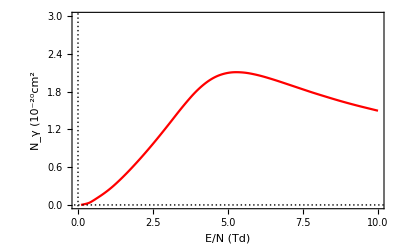

```mathematica
ElectronERange1 = Range[0, 30, 0.1]; 
PhotonWRange1 = Range[(2*Pi*hc)/(10*1000), 30, 0.1]; 
dsdwFaster[En, ω] = Piecewise[{{dsdwTable[En, ω], En > ω}, {0, True}}]; 
tabulatedData = ParallelTable[dsdwFaster[En, ω], {En, ElectronERange1}, {ω, PhotonWRange1}]
```

### Export tabulated cross section

```mathematica
(* Memoization means that dsdw is evaluated only once for each unique [En, ω] passed to dsdwMemoized *)
(* There is, however, an issue with momization and parallel computations, see
 https://mathematica.stackexchange.com/questions/1259/parallelize-evaluation-of-function-with-memoization *)
dsdwMemoized[En_, ω_]:=Parallel`Developer`SendBack[dsdwMemoized[En, ω]=  dsdw[En,ω, False]]
SetSharedFunction[dsdwMemoized]

GenerateCPPData[EnergyScale_, λmax_] := Module[ {EnRange, cppData, ωmin, wRange1, wRange2, wRange, dataRow, cppDataLock},
EnRange = Join[Range[0, 2, 0.1 EnergyScale], Range[2, 30, 0.2 EnergyScale]] //Sort // DeleteDuplicates;
cppData = {}; (* Data structure compatible with c++ geant4 simulation code (FunctionTable.cpp) *)
SetSharedVariable[cppData];
ParallelDo[
ωmin=(2π hc)/λmax;
wRange1=Range[ωmin,En,0.1EnergyScale];
wRange2=Subdivide[ωmin,En,20/EnergyScale];
wRange = If[Length[wRange1]>Length[wRange2], wRange1, wRange2];
dataRow = Table[{ω, dsdwMemoized[En, ω]}, {ω,wRange}];
CriticalSection[cppDataLock,AppendTo[cppData, {En, dataRow}]];
,{En,EnRange}];
Return[Sort[cppData,#1[[1]]<#2[[1]]&]]; (* Sort by electron energy *)
];
ExportCPPData[cppData_, filename_] := Module[{},
file=FileNameJoin[{NotebookDirectory[], filename}];
BinaryWrite[file, Length[cppData], "UnsignedInteger64"];
Do[
BinaryWrite[file, entry[[1]], "Real64"];
BinaryWrite[file, Length[entry[[2]]], "UnsignedInteger64"];
BinaryWrite[file, Flatten[entry[[2]]], "Real64"];
, {entry,cppData}];
Close[file];
];
AbsoluteTiming[
data = GenerateCPPData[1.0, 10000(* Angstrom *)];
ExportCPPData[data, "XS_NBrS_table_no_pol.dat"];
data = GenerateCPPData[2.0, 10000(* Angstrom *)];
ExportCPPData[data, "XS_NBrS_table_no_pol_sparse.dat"];
]
```

```mathematica
(* Memoization means that dsdw is evaluated only once for each unique [En, ω] passed to dsdwMemoized *)
(* There is, however, an issue with momization and parallel computations, see
 https://mathematica.stackexchange.com/questions/1259/parallelize-evaluation-of-function-with-memoization *)
wdsdwMemoized[En_, ω_]:=Parallel`Developer`SendBack[wdsdwMemoized[En, ω]=  wdsdw[En,ω, True]]
SetSharedFunction[dsdwMemoized]

GenerateXStable[En_] := Module[ {EnRange, DataTable, ωmin, wRange1, wRange2, wRange, dataRow, cppDataLock},
wRange = Subdivide[0,En,100];
DataTable = ParallelTable[{ω, 10^8 wdsdwMemoized[En, sω] (* A^2 to barn *)}, {ω,wRange}];
Return[DataTable];
];
PrintXStable[En_] := Module[{DataTable, filename},
DataTable = GenerateXStable[En];
filename=FileNameJoin[{NotebookDirectory[], StringJoin[{"Mathem_wdsdw_with_pol_", ToString[NumberForm[En, {3,1}]], "_eV.dat"}]}];
Export[filename, DataTable, "Table"];
];
AbsoluteTiming[
PrintXStable[0.5];
PrintXStable[2.0];
PrintXStable[4.0];
PrintXStable[10.0];
]
```